```mathematica
fmass={0.51,0,105.66,0,1776.99,0,2.3,4.8,1270.,95.,173210.,4180.}*1*10^-4;
mv={80.42,91.19};
mh=125.09;
thetaW=28.76*π/180;
sw2=Sin[thetaW]^2;
ga={-0.5,0.5,-0.5,0.5,-0.5,0.5,0.5,-0.5,0.5,-0.5,0.5,-0.5};
gv={0.5,-0.5+2*sw2,0.5,-0.5+2*sw2,0.5,-0.5+2*sw2,0.5-4*sw2/3.,-0.5+2*sw2/3.,0.5-4*sw2/3.,-0.5+2*sw2/3.,0.5-4*sw2/3.,-0.5+2*sw2/3.};
gs=1.214 ;
v=246;
alphas=gs^2/(4.*π) ;
GF=1.16*10^-4;
g=8*mv[[1]]^2/(√2)*GF;
PMNS=0.5Transpose[{{0.799+0.844,0.242+0.494,0.284+0.521},{0.516+0.582,0.467+0.678,0.490+0.695},{0.141+0.156,0.639+0.774,0.615+0.754}}];
CKM=Transpose[{{0.97,0.22,0.0087},{0.22,0.97,0.04},{0.0035,0.041,0.999}}];
Mp=2.4*10^19;
kappa=1./Mp ;
DMMass1=Table[i,{i,1,1000,10^1}];
DMMass2=Table[i,{i,10^3,10^6,10^4}];
DMMass=Catenate[{DMMass1,DMMass2}];
cota1=4*10^16;
cota2=1*10^23;
Print[Length[DMMass]]
```

35

```mathematica
xh[m_]:=mh^2/m^2
xw[m_]:=mv[[1]]^2/m^2
xz[m_]:=mv[[2]]^2/m^2
xf[m_]:=fmass^2/m^2
```

```mathematica
Φ[s_,θ12_,ϕ12_,θ3_,ϕ3_,m_,m1_,m2_,m3_]:=1/(8^2(2π)^5)(1-2*(m1^2+m2^2)/s+((m1^2-m2^2)^2)/s^2)^(1/2)(1-2*(s+m3^2)/m^2+((s-m3^2)^2)/m^4)^(1/2) Sin[θ12]Sin[θ3]
```

```mathematica
dqqg[s_,θ12_,ϕ12_,θ3_,ϕ3_,m_,m1_,m2_,m3_,ξ_]:=(ξ^2 Mp^2 kappa^4)/(2m)16*72*gs^2*((s-m1^2-m2^2)/2-m1^2)*Φ[s,θ12,ϕ12,θ3,ϕ3,m,m1,m2,m3]
dffxw[s_,θ12_,ϕ12_,θ3_,ϕ3_,m_,m1_,m2_,m3_,ξ_]:=(ξ^2 Mp^2 kappa^4)/(2m)18*g^2*(s-m1^2-m2^2)/2*Φ[s,θ12,ϕ12,θ3,ϕ3,m,m1,m2,m3]
dffxz[s_,θ12_,ϕ12_,θ3_,ϕ3_,m_,m1_,m2_,m3_,i_,ξ_]:=(ξ^2 Mp^2 kappa^4)/(2m)72*(ga[[i]]^2+gv[[i]]^2)(s-m1^2-m2^2)/2*Φ[s,θ12,ϕ12,θ3,ϕ3,m,m1,m2,m3]
```

```mathematica
Gamma1=Table[0,{i,1,Length[DMMass]}];
Gamma2=Table[0,{i,1,Length[DMMass]}];
Gamma3=Table[0,{i,1,Length[DMMass]}];
Gamma4=Table[0,{i,1,Length[DMMass]}];
Gamma5=Table[0,{i,1,Length[DMMass]}];
Gamma6=Table[0,{i,1,Length[DMMass]}];
Gamma7=Table[0,{i,1,Length[DMMass]}];
```

```mathematica
qqg[m_,m1_,m2_,m3_,ξ_]:=NIntegrate[dqqg[s,θ12,ϕ12,θ3,ϕ3,m,m1,m2,m3,ξ],{s,(m1+m2)^2,(m-m3)^2},{θ12,0,π},{θ3,0,π},{ϕ12,0,2π},{ϕ3,0,2π}]
ffxw[m_,m1_,m2_,m3_,ξ_]:=NIntegrate[dffxw[s,θ12,ϕ12,θ3,ϕ3,m,m1,m2,m3,ξ],{s,(m1+m2)^2,(m-m3)^2},{θ12,0,π},{θ3,0,π},{ϕ12,0,2π},{ϕ3,0,2π}]
ffxz[m_,m1_,m2_,m3_,i_,ξ_]:=NIntegrate[dffxz[s,θ12,ϕ12,θ3,ϕ3,m,m1,m2,m3,i,ξ],{s,(m1+m2)^2,(m-m3)^2},{θ12,0,π},{θ3,0,π},{ϕ12,0,2π},{ϕ3,0,2π}]
```

```mathematica
hh[m_,ξ_]:=(ξ^2 Mp^2 kappa^4)/(32π)m^3(1+2*xh[m])^2(1-4*xh[m])^(1/2)
zz[m_,ξ_]:=(ξ^2 Mp^2 kappa^4)/(32π)m^3(1-4*xz[m]+12*xz[m]^2)*(1-4*xz[m])^(1/2)
ww[m_,ξ_]:=(ξ^2 Mp^2 kappa^4)/(16π)m^3(1-4*xw[m]+12*xw[m]^2)*(1-4*xw[m])^(1/2)
ffx[m_,m1_,ξ_]:=(ξ^2 Mp^2 kappa^4)/(8π)m*m1^2(1-4*m1^2/m^2)^(3/2)*9
```

```mathematica
ξ=1;
For[i=0,i<Length[DMMass],i++,{
m=DMMass[[i+1]];

If[m>2*mh,Gamma1[[i+1]]=hh[m,ξ]];

If[m>2*mv[[2]],Gamma2[[i+1]]=zz[m,ξ]];

If[m>2*mv[[1]],Gamma3[[i+1]]=ww[m,ξ]];

For[ii=0,ii<12,ii++,{
If[m>2*fmass[[ii+1]],Gamma4[[i+1]]+=ffx[m,fmass[[ii+1]],ξ]]}];

For[ii=5,ii<12,ii++,{
	If[m>2*fmass[[ii+1]],Gamma5[[i+1]]+=qqg[m,fmass[[ii+1]],fmass[[ii+1]],0,ξ]]}];

For[ii=0,ii<3,ii++,{
For[jj=0, jj<3, jj++,{
	If[m>fmass[[2*ii+7]]+fmass[[2*jj+8]]+mv[[1]],Gamma6[[i+1]]+=ffxw[m,fmass[[2*ii+7]],fmass[[2*jj+8]],mv[[1]],ξ]*(CKM[[ii+1]][[jj+1]])^2]}];}]

For[ii=0,ii<3,ii++,{
For[jj=0, jj<3, jj++,{
	If[m>fmass[[2*ii+1]]+fmass[[2*jj+2]]+mv[[1]],Gamma6[[i+1]]+=ffxw[m,fmass[[2*ii+1]],fmass[[2*jj+2]],mv[[1]],ξ]*(PMNS[[ii+1]][[jj+1]])^2]}];}]

For[ii=0,ii<12,ii++,{
	If[m>2*fmass[[ii+1]]+mv[[2]],Gamma7[[i+1]]+=ffxz[m,fmass[[ii+1]],fmass[[ii+1]],mv[[2]],ii+1,ξ]]}];
}]
```

```mathematica
Gammatot=Gamma1+Gamma2+Gamma3+Gamma4+Gamma5+Gamma6+Gamma7;
```

```mathematica
BR1=Table[{DMMass[[i]],Gamma1[[i]]/Gammatot[[i]]},{i,1,Length[DMMass]}];
BR2=Table[{DMMass[[i]],Gamma2[[i]]/Gammatot[[i]]},{i,1,Length[DMMass]}];
BR3=Table[{DMMass[[i]],Gamma3[[i]]/Gammatot[[i]]},{i,1,Length[DMMass]}];
BR4=Table[{DMMass[[i]],Gamma4[[i]]/Gammatot[[i]]},{i,1,Length[DMMass]}];
BR5=Table[{DMMass[[i]],Gamma5[[i]]/Gammatot[[i]]},{i,1,Length[DMMass]}];
BR6=Table[{DMMass[[i]],Gamma6[[i]]/Gammatot[[i]]},{i,1,Length[DMMass]}];
BR7=Table[{DMMass[[i]],Gamma7[[i]]/Gammatot[[i]]},{i,1,Length[DMMass]}];
```

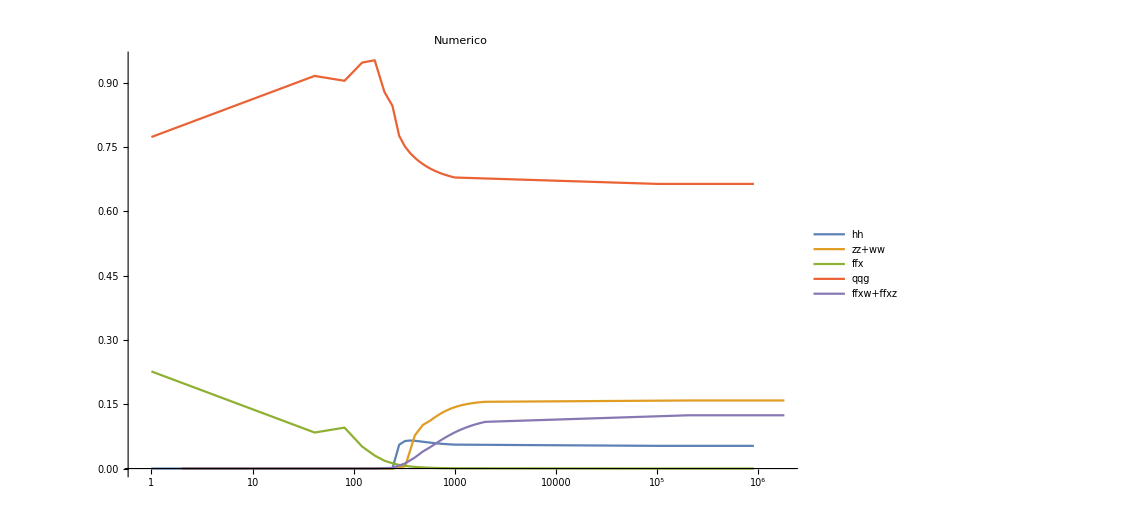

```mathematica
ListLogLinearPlot[{BR1,BR2+BR3,BR4,BR5,BR6+BR7},ImageSize->Large,PlotLegends->Placed[{"hh","zz+ww","ffx","qqg","ffxw+ffxz"},{0.75,0.50}],Joined->True,GridLines->Automatic,PlotRange->Full,PlotLabel->"Numerico"]
```